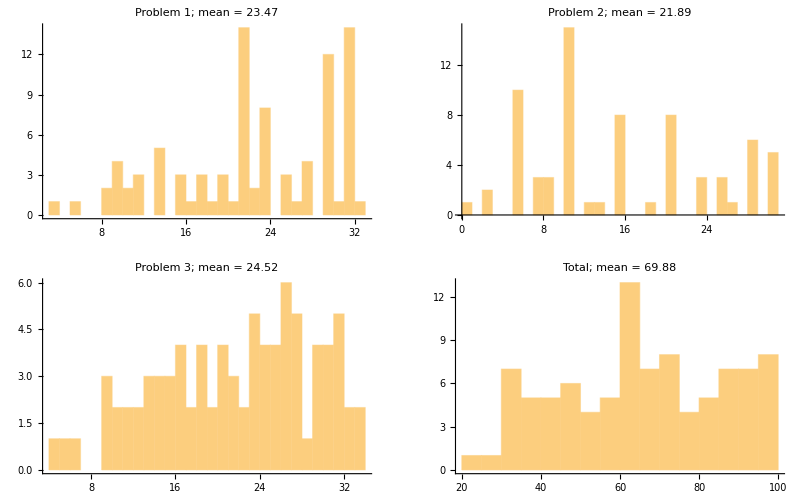

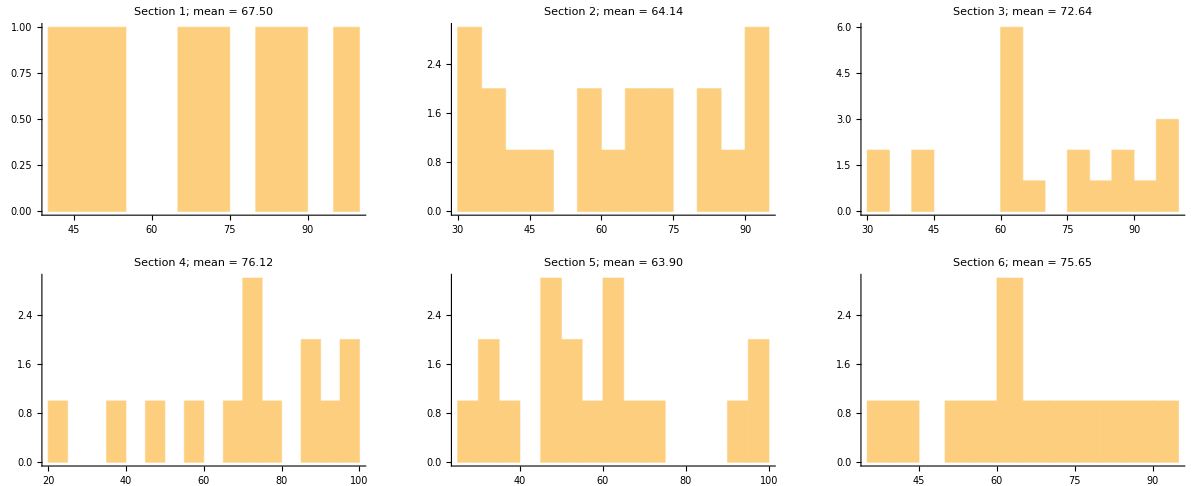

```mathematica
(*GradeReport.nb revision 26/9/2016. Written and maintained by Charles Hussong chussong@jhu.edu*)

(*Takes grade data in a spreadsheet and outputs histograms of students' performance on each problem and on the overall exam. Expected data format is: names in first two columns, then each student's section number in third column, then problem's score in subsequent columns, followed by a column of the totals. The top row is expected to be used for column labels and is not read.*)

(*Students whose problem scores are all blank will be treated as bad data and removed irrespective of their score in the "total" column. No other data alterations are made.*)

ClearAll["Global`*"];
problems=3;
students=114;
sections=6; (*0 = skip section computations and ignore third column*)
maxpoints={33,33,34,100};  (*last entry is max points for exam*)
totalBinSize=5; (*bin size for total-score histogram*)
dataname="mid1grades.ods";
exportName="mid1histograms.pdf";
SetDirectory["~/Dropbox/Classes/171.102/1617F/Data"];

(*--------------------------------------------------------------------------*)

(*Data reading and cleanup*)
blankCondition={_,_,_};
Do[blankCondition=Append[""]@blankCondition,problems];
blankCondition=Append[_]@blankCondition;
hist=ConstantArray[0,problems+1];
data=Take[Import[dataname,{"Data",1}],{2,students+1}];
Do[data[[i]]=Take[data[[i]],{1,problems+4}],{i,1,students}];
students-=Length[Cases[blankCondition]@data];
data=DeleteCases[blankCondition]@data;

(*Whole-class analysis and visualization*)
classMean=Mean@data[[All,problems+4]];
classMean=N[classMean,IntegerLength@Round@classMean+2];
classStDev=StandardDeviation@data[[All,problems+4]];
classStDev=N[classStDev,IntegerLength@Round@classStDev+2];
classMedian=Median@data[[All,problems+4]];
maxCount=ConstantArray[0,problems+1];
Do[maxCount[[i]]=Max@BinCounts[data[[All,3+i]],1];,{i,1,problems}];
maxCount[[problems+1]]=Max@BinCounts[data[[All,4+problems]],totalBinSize];
Do[
hist[[i]]=Histogram[data[[All,3+i]],{0,maxpoints[[i]],1},PlotLabel->"Problem "<>ToString[i]<>"; mean = "<>ToString@N[Mean@data[[All,3+i]],4],AxesOrigin->0,PlotRange->Max@maxCount];
,{i,1,problems}]
totalEndpoint=maxpoints[[problems+1]]-Mod[maxpoints[[problems+1]],totalBinSize];
hist[[problems+1]]=Histogram[data[[All,problems+4]],{0,totalEndpoint,totalBinSize},PlotLabel->"Total; mean = "<>ToString@N[Mean@data[[All,4 + problems]],4],AxesOrigin->0,PlotRange-> Max@maxCount];
columns=Ceiling@Sqrt@(problems+1);
rows=Ceiling@((problems+1)/columns);
histGrid=ConstantArray[0,{rows,columns}];
pos={1,1};
Do[histGrid[[pos[[1]],pos[[2]]]]=hist[[i]];
pos[[2]]++;
If[pos[[2]]>columns,
pos[[1]]++;
pos[[2]]=1;
];
,{i,1,problems+1}];
Print[GraphicsGrid[histGrid,ImageSize->Full]];

(*Section analysis and visualization*)
If[sections≠0,
secData=Table[{},sections];secHist=ConstantArray[0,sections];
sectionMeans=ConstantArray[0,sections];
sectionMaxCount=ConstantArray[0,sections];
scoreVectors=data[[All,Range[3,problems+4]]];
Do[If[scoreVectors[[row]][[1]]>0,
secData[[scoreVectors[[row]][[1]]]]=Append[secData[[scoreVectors[[row]][[1]]]],scoreVectors[[row]][[Range[2,problems+2]]]];
];
,{row,1,students}];
Do[sectionMaxCount[[i]]=Max@BinCounts[secData[[i]][[All,problems+1]],totalBinSize];,{i,1,sections}];
Do[sectionMeans[[i]]=Mean@secData[[i]][[All,problems+1]];
sectionMeans[[i]]=N[sectionMeans[[i]],IntegerLength@Round@sectionMeans[[i]]+2];
secHist[[i]]=Histogram[secData[[i]][[All,problems+1]],{0,totalEndpoint,totalBinSize},PlotRange->Max@sectionMaxCount,PlotLabel-> "Section "<>ToString[i]<>"; mean = "<>ToString[sectionMeans[[i]]]];
,{i,1,sections}];
secColumns=Ceiling@Sqrt@(sections);
secRows=Ceiling@(sections/secColumns);
secHistGrid=ConstantArray["",{secRows,secColumns}];
pos={1,1};
Do[secHistGrid[[pos[[1]],pos[[2]]]]=secHist[[i]];
pos[[2]]++;
If[pos[[2]]>secColumns,
pos[[1]]++;
pos[[2]]=1;
];
,{i,1,sections}];
Print[GraphicsGrid[secHistGrid,ImageSize->Full]];
];

(*Create and export PDF report*)
report=CreateDocument[];
SetOptions[report,PageHeaders->{{None,None,None},{None,None,None}},PageFooters->{{None,None,None},{None,None,None}},PrintingOptions->{"PaperOrientation"->"Landscape","PrintingMargins"->{{20,20},{40,40}}}];
Paste[report,GraphicsGrid[histGrid,ImageSize->Full]];Paste[report,Framed["Additional statistics:\t\t St.Dev. = "<>ToString@classStDev<>"\t\t median = "<>ToString@classMedian]];
If[sections≠0,Paste[report,GraphicsGrid[secHistGrid,ImageSize->Full]]];
Export[exportName,report];
NotebookClose[report];
```